```mathematica
edgeCoordinates=PixelValuePositions[EdgeDetect[Import["/Users/tarachari/Desktop/Screen Shot 2021-06-08 at 8.11.27 AM.png"]],1];
```

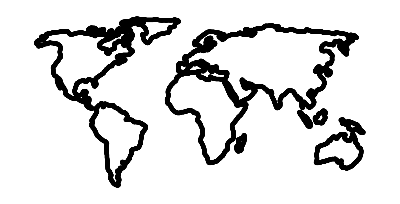

```mathematica
Graphics[Point[edgeCoordinates]]
```

```mathematica
Dimensions[edgeCoordinates]
```

{16087,2}

```mathematica
pointcloud=RandomPoint[Point[edgeCoordinates],700];
```

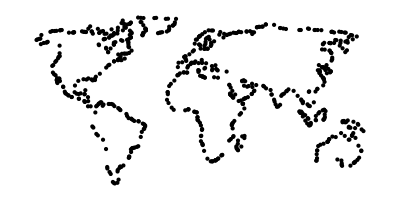

```mathematica
Graphics[Point[pointcloud]]
```

```mathematica
pointcloud
```

{{369.,927.},{416.,921.},{1764.,715.},{1476.,525.},{1024.,745.},{1670.,387.},{475.,714.},{146.,869.},{1411.,604.},{1268.,426.},{1686.,565.},{1135.,932.},{1197.,628.},{694.,1000.},{385.,383.},{1754.,248.},{1885.,406.},{1046.,356.},{548.,44.},{1913.,872.},{445.,505.},{1199.,229.},{283.,926.},{368.,525.},{1129.,156.},{295.,929.},{457.,918.},{1879.,158.},{1342.,940.},{610.,1001.},{520.,857.},{1777.,932.},{295.,626.},{1739.,232.},{473.,203.},{1955.,315.},{1962.,144.},{1114.,722.},{1923.,899.},{657.,236.},{1965.,292.},{1863.,877.},{461.,277.},{624.,908.},{1067.,718.},{194.,805.},{1304.,918.},{1927.,903.},{1688.,568.},{193.,599.},{890.,652.},{1060.,749.},{1236.,322.},{991.,806.},{1100.,843.},{1854.,877.},{732.,882.},{767.,908.},{1880.,143.},{984.,740.},{1663.,508.},{1514.,525.},{1058.,921.},{504.,944.},{388.,386.},{747.,902.},{1281.,223.},{545.,930.},{1841.,304.},{1345.,603.},{586.,146.},{1978.,159.},{1007.,448.},{1461.,577.},{520.,851.},{1021.,436.},{1132.,718.},{768.,909.},{1022.,396.},{1353.,592.},{1771.,459.},{712.,935.},{465.,276.},{622.,223.},{1957.,309.},{1164.,892.},{627.,920.},{1711.,527.},{1058.,824.},{1903.,306.},{1795.,729.},{1069.,728.},{192.,817.},{1350.,933.},{419.,485.},{1440.,577.},{1110.,149.},{611.,883.},{551.,940.},{1296.,270.},{1180.,629.},{607.,850.},{975.,729.},{696.,890.},{179.,863.},{1133.,705.},{1263.,279.},{470.,710.},{120.,866.},{1970.,901.},{1714.,501.},{193.,597.},{541.,878.},{1949.,882.},{696.,890.},{1227.,540.},{1108.,870.},{1199.,910.},{1995.,182.},{692.,989.},{559.,879.},{1053.,917.},{567.,877.},{1590.,579.},{1564.,581.},{1298.,525.},{1741.,939.},{1363.,577.},{1651.,498.},{600.,948.},{435.,675.},{297.,536.},{1197.,684.},{1777.,461.},{1767.,822.},{1571.,584.},{1068.,728.},{1847.,295.},{1817.,283.},{1160.,180.},{187.,772.},{1082.,936.},{101.,907.},{822.,928.},{1219.,550.},{588.,885.},{1641.,521.},{405.,338.},{1716.,552.},{435.,922.},{1811.,283.},{1818.,860.},{1976.,156.},{895.,993.},{419.,922.},{1733.,579.},{1764.,842.},{183.,618.},{1038.,906.},{192.,611.},{1770.,717.},{443.,507.},{1754.,248.},{495.,55.},{699.,885.},{213.,604.},{901.,996.},{590.,925.},{547.,928.},{1235.,298.},{1762.,938.},{1163.,912.},{611.,175.},{1694.,390.},{1363.,937.},{1799.,743.},{544.,84.},{1774.,820.},{547.,930.},{972.,728.},{543.,790.},{1908.,383.},{309.,931.},{1179.,205.},{168.,934.},{406.,912.},{261.,538.},{1662.,938.},{589.,927.},{838.,508.},{320.,932.},{1254.,234.},{1928.,397.},{993.,454.},{1762.,663.},{616.,805.},{492.,894.},{622.,223.},{1070.,867.},{1913.,920.},{607.,1000.},{1770.,390.},{1503.,969.},{1766.,937.},{1298.,525.},{514.,490.},{567.,781.},{1771.,395.},{1049.,740.},{441.,840.},{1547.,945.},{943.,684.},{1047.,336.},{475.,191.},{764.,907.},{1177.,911.},{1179.,206.},{1181.,633.},{1858.,294.},{112.,907.},{97.,893.},{1728.,697.},{681.,302.},{582.,888.},{680.,286.},{1968.,282.},{1898.,864.},{1753.,719.},{1900.,851.},{860.,613.},{569.,938.},{1088.,647.},{1015.,444.},{367.,497.},{435.,844.},{1214.,916.},{614.,804.},{676.,1013.},{1242.,557.},{1890.,407.},{1753.,246.},{1441.,972.},{593.,917.},{771.,910.},{478.,891.},{352.,499.},{1643.,430.},{497.,943.},{511.,743.},{678.,279.},{1041.,837.},{1656.,431.},{598.,881.},{1843.,877.},{736.,886.},{1915.,804.},{704.,878.},{414.,315.},{674.,257.},{1233.,292.},{128.,927.},{1199.,235.},{725.,873.},{559.,795.},{1488.,494.},{1855.,163.},{1297.,311.},{1746.,147.},{170.,668.},{665.,1014.},{953.,749.},{604.,948.},{565.,453.},{1772.,254.},{1438.,972.},{1048.,701.},{904.,727.},{564.,796.},{1347.,938.},{2001.,209.},{1946.,886.},{1043.,747.},{557.,117.},{1804.,274.},{1768.,822.},{1915.,387.},{439.,842.},{406.,926.},{1065.,827.},{620.,406.},{772.,910.},{1229.,923.},{361.,537.},{628.,402.},{458.,883.},{609.,887.},{458.,492.},{1549.,945.},{1922.,371.},{288.,606.},{1031.,826.},{426.,492.},{1188.,220.},{824.,1006.},{1243.,395.},{942.,695.},{527.,866.},{309.,635.},{495.,907.},{572.,451.},{575.,452.},{1256.,921.},{321.,519.},{1947.,312.},{1190.,905.},{1515.,500.},{956.,459.},{1651.,936.},{650.,393.},{1132.,716.},{582.,137.},{920.,685.},{1282.,227.},{983.,690.},{833.,930.},{222.,939.},{1881.,141.},{615.,975.},{1259.,494.},{539.,942.},{1078.,934.},{1842.,923.},{591.,953.},{599.,159.},{542.,937.},{1637.,533.},{1232.,343.},{459.,834.},{607.,890.},{173.,665.},{640.,988.},{613.,976.},{635.,396.},{285.,594.},{666.,987.},{476.,714.},{1071.,887.},{1098.,900.},{1672.,948.},{554.,953.},{614.,804.},{346.,637.},{714.,1008.},{454.,280.},{891.,990.},{354.,489.},{1138.,159.},{481.,718.},{526.,866.},{1267.,928.},{934.,742.},{617.,977.},{889.,989.},{59.,880.},{1520.,538.},{1839.,870.},{606.,840.},{1199.,590.},{1513.,520.},{1803.,271.},{1302.,470.},{388.,391.},{292.,620.},{458.,834.},{1810.,817.},{1914.,920.},{426.,921.},{966.,687.},{547.,53.},{1673.,384.},{1174.,892.},{360.,484.},{1297.,463.},{623.,811.},{1798.,737.},{1615.,549.},{485.,493.},{541.,747.},{1436.,584.},{925.,694.},{506.,736.},{1285.,646.},{1811.,930.},{1537.,556.},{193.,647.},{868.,469.},{955.,458.},{401.,431.},{613.,832.},{1175.,921.},{648.,393.},{1037.,844.},{1055.,838.},{1848.,295.},{367.,954.},{1258.,519.},{414.,317.},{1699.,375.},{1649.,422.},{1052.,726.},{1875.,860.},{1644.,493.},{709.,946.},{1029.,695.},{854.,606.},{1683.,369.},{682.,305.},{1925.,279.},{438.,500.},{1879.,146.},{421.,486.},{1917.,919.},{328.,567.},{1941.,125.},{1041.,827.},{397.,350.},{1914.,841.},{949.,780.},{1375.,608.},{1045.,745.},{407.,955.},{245.,930.},{1063.,198.},{610.,896.},{501.,45.},{1785.,455.},{1302.,304.},{1881.,927.},{974.,689.},{59.,880.},{669.,980.},{1642.,519.},{1307.,482.},{1736.,179.},{1378.,956.},{430.,671.},{1303.,498.},{340.,638.},{1158.,913.},{1069.,876.},{1065.,847.},{1024.,681.},{1183.,631.},{947.,777.},{1999.,226.},{1715.,563.},{1739.,697.},{1180.,206.},{1239.,526.},{686.,319.},{471.,499.},{1771.,604.},{1802.,706.},{887.,987.},{1346.,940.},{960.,712.},{583.,997.},{277.,534.},{1449.,573.},{1166.,650.},{503.,730.},{1501.,950.},{1734.,939.},{470.,709.},{544.,921.},{622.,984.},{1286.,648.},{1016.,751.},{1041.,366.},{1768.,600.},{1724.,413.},{1273.,496.},{1922.,901.},{616.,894.},{538.,475.},{617.,406.},{884.,984.},{1963.,348.},{1678.,950.},{1703.,939.},{511.,929.},{396.,960.},{928.,745.},{1181.,211.},{1663.,938.},{1292.,622.},{339.,539.},{1862.,305.},{1037.,376.},{701.,963.}}

```mathematica
Export["/Users/tarachari/Desktop/mapPoints700.csv",pointcloud,"CSV"]
```

/Users/tarachari/Desktop/mapPoints700.csv